```mathematica
d
```

```mathematica
Plot3D[h+r*x-x^2/. h->1,{x,-10,10},{r,-10,10}]
```

-Graphics3D-

```mathematica
ContourPlot3D[h+r*x-x^2==0,{h,-20,20},{r,-10,10},{x,-20,20},AxesLabel->{h,r,x},ImageSize->500]
```

-Graphics3D-

```mathematica
Show[%17,ViewPoint->Below]
```

-Graphics3D-

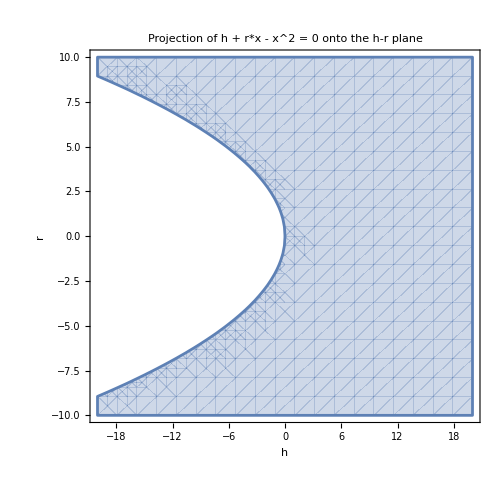

```mathematica
RegionPlot[r^2+4h>=0,{h,-20,20},{r,-10,10},AxesLabel->{h,r},ImageSize->500,FrameLabel->{"h","r"},PlotLabel->"Projection of h + r*x - x^2 = 0 onto the h-r plane"]
```

```mathematica
x[t_,ε_]:=(-4 ε+Sqrt[1-4 ε]+1)/(2-8 ε) Exp[-(Sqrt[1-4 ε]+1)/(2 ε) t]+(4 ε+Sqrt[1-4 ε]-1)/(2+8 ε) Exp[(-1+Sqrt[1-4 ε])/(2 ε) t]

Manipulate[Plot[x[ t,ϵ],{t,0,1},PlotRange->All,AxesLabel->{"t","x(t)"},PlotLabel->"Plot of x(t) for given ϵ",Epilog->{Dashed,Red,Line[{{ϵ/(1-ϵ),-10^6},{ϵ/(1-ϵ),10^6}}],
Dashed,Blue,Line[{{1,-10^6},{1,10^6}}]
}],
{{ϵ,0.1,"ϵ"},0,0.5,0.01}]
```

```mathematica
x[t_,ε_]:=(4 ε+Sqrt[1-4 ε]-1)/(2+8 ε) Exp[(-1+Sqrt[1-4 ε])/(2 ε) t]
Manipulate[Plot[x[ t,ϵ],{t,0,1},PlotRange->All,AxesLabel->{"t","x(t)"},PlotLabel->"Plot of x(t) for given ϵ",Epilog->{Dashed,Blue,Line[{{1,-10^6},{1,10^6}}]
}],
{{ϵ,0.1,"ϵ"},0,0.5,0.01}]
```

```mathematica
x[t_,ε_]:=(-4 ε+Sqrt[1-4 ε]+1)/(2-8 ε) Exp[-(Sqrt[1-4 ε]+1)/(2 ε) t]
Manipulate[Plot[x[ t,ϵ],{t,0,1},PlotRange->All,AxesLabel->{"t","x(t)"},PlotLabel->"Plot of x(t) for given ϵ",
Epilog->{Dashed,Red,Line[{{ϵ/(1-ϵ),-10^6},{ϵ/(1-ϵ),10^6}}]
}],
{{ϵ,0.1,"ϵ"},0,0.5,0.01}]
```